```mathematica
GLargeNfreal=-(ⅈ ⅇ^(-(Abs[x]^(1/3) Gamma[2/3])/(3 2^(2/3) √3 Nfkf^(1/3) π^(5/3) v^(4/3) (1/v+(ⅈ τ)/x)^(2/3))))/(2 π (x+ⅈ v τ));
```

```mathematica
GLargeNfreal/.{v->1,x->1.2,τ->.3,Nfkf->1}
```

-0.0299329-0.121866 ⅈ

```mathematica
GLargeNfOtherNotebook=-Cos[(ω √(ⅈ kxv+ω) Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkfv π^(5/2) (kxv-ⅈ ω)^2)]/(kxv-ⅈ ω)+(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkfv π^5 (ⅈ kxv+ω)^3)])/(2 2^(2/3) √3 π^(5/3) (Nfkfv ω)^(1/3) (ⅈ kxv+ω)^2)-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkfv π^5 (ⅈ kxv+ω)^3)])/(48 2^(1/3) √3 π^(13/3) (kxv-ⅈ ω)^3 (Nfkfv ω)^(2/3));
```

```mathematica
GLargeNfOtherNotebookFixed=GLargeNfOtherNotebook/.{ω->-ω,kxv->-kx,Nfkfv->Nfkf}
```

-Cos[(√(-ⅈ kx-ω) ω Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx+ⅈ ω)^2)]/(-kx+ⅈ ω)-(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(2 2^(2/3) √3 π^(5/3) (-ⅈ kx-ω)^2 (-Nfkf ω)^(1/3))-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx+ⅈ ω)^3 (-Nfkf ω)^(2/3))

```mathematica
(-Cos[(√(-ⅈ kx-ω) ω Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx+ⅈ ω)^2)]/(-kx+ⅈ ω)-(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(2 2^(2/3) √3 π^(5/3) (-ⅈ kx-ω)^2 (-Nfkf ω)^(1/3))-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx+ⅈ ω)^3 (-Nfkf ω)^(2/3))/.{ω->-ω})*
```

Conjugate[-Cos[(ω √(-ⅈ kx+ω) Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx-ⅈ ω)^2)]/(-kx-ⅈ ω)+(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx+ω)^3)])/(2 2^(2/3) √3 π^(5/3) (Nfkf ω)^(1/3) (-ⅈ kx+ω)^2)-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx+ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx-ⅈ ω)^3 (Nfkf ω)^(2/3))]

Minus sign, why?

```mathematica
GLargeNfv1[ω_,kx_,Nfkf_]:=-If[ω<0,-Cos[(√(-ⅈ kx-ω) ω Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx+ⅈ ω)^2)]/(-kx+ⅈ ω)-(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(2 2^(2/3) √3 π^(5/3) (-ⅈ kx-ω)^2 (-Nfkf ω)^(1/3))-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx-ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx+ⅈ ω)^3 (-Nfkf ω)^(2/3)),Conjugate[-Cos[(ω √(-ⅈ kx+ω) Gamma[2/3]^(3/2))/(18 3^(1/4) √Nfkf π^(5/2) (-kx-ⅈ ω)^2)]/(-kx-ⅈ ω)+(ⅈ ω HypergeometricPFQ[{1},{5/6,4/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx+ω)^3)])/(2 2^(2/3) √3 π^(5/3) (Nfkf ω)^(1/3) (-ⅈ kx+ω)^2)-(ω^2 Gamma[-1/3] Gamma[2/3]^2 HypergeometricPFQ[{1},{7/6,5/3},-(ω^2 Gamma[2/3]^3)/(1296 √3 Nfkf π^5 (-ⅈ kx+ω)^3)])/(48 2^(1/3) √3 π^(13/3) (-kx-ⅈ ω)^3 (Nfkf ω)^(2/3))]]
```

```mathematica
test={v->1,Nfkf->.01,ω->1.,kx->.3};
nint=GLargeNfreal Exp[ⅈ ω τ-ⅈ kx x]/.test;
```

```mathematica
xint[τi_?NumericQ]:=NIntegrate[nint/.τ->τi,{x,-∞,0,∞},Method->"LevinRule",MaxRecursion->20, PrincipalValue->True]
τint[xi_?NumericQ]:=NIntegrate[nint/.x->xi,{τ,-∞,0,∞},Method->"LevinRule",MaxRecursion->20, PrincipalValue->True]
```

```mathematica
200/2^15//N
```

0.00610352

```mathematica
τs=Table[τi,{τi,-50,50,.03}];
vv=ParallelTable[xint[τi],{τi,τs}];
xintIP=Interpolation[{τs,vv}ᵀ];
```

$Aborted

Transpose::nmtx: The first two levels of {{-50.,-49.97,-49.94,-49.91,-49.88,-49.85,-49.82,-49.79,-49.76,-49.73,-49.7,-49.67,-49.64,-49.61,-49.58,-49.55,-49.52,-49.49,-49.46,-49.43,-49.4,-49.37,«7»,-49.13,-49.1,-49.07,-49.04,-49.01,-48.98,-48.95,-48.92,-48.89,-48.86,-48.83,-48.8,-48.77,-48.74,-48.71,-48.68,-48.65,-48.62,-48.59,-48.56,-48.53,«3284»},vv} cannot be transposed.

Interpolation::innd: First argument in Transpose[{{-50.,-49.97,-49.94,-49.91,-49.88,-49.85,-49.82,-49.79,-49.76,-49.73,-49.7,-49.67,-49.64,-49.61,-49.58,-49.55,-49.52,-49.49,-49.46,-49.43,-49.4,«9»,-49.1,-49.07,-49.04,-49.01,-48.98,-48.95,-48.92,-48.89,-48.86,-48.83,-48.8,-48.77,-48.74,-48.71,-48.68,-48.65,-48.62,-48.59,-48.56,-48.53,«3284»},vv}] does not contain a list of data and coordinates.

```mathematica
xs=Table[xi,{xi,-50,50,.03}];
vv2=ParallelTable[τint[xi],{xi,xs}];
τintIP=Interpolation[{xs,vv2}ᵀ];
```

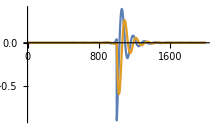

```mathematica
ListLinePlot[ReIm[vv]ᵀ,PlotRange->All]
```

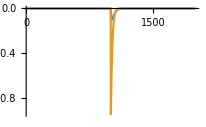

```mathematica
ListLinePlot[ReIm[vv2]ᵀ,PlotRange->All]
```

```mathematica
1/NIntegrate[τintIP[τ],{τ,-30,0,30},PrincipalValue->True]-1/Gf0[ω,kx]/.test
```

0.00159137+0.12956 ⅈ

```mathematica
1/NIntegrate[τintIP[τ],{τ,-50,0,50},PrincipalValue->True]-1/Gf0[ω,kx]/.test
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in τ near {τ} = {-1.51461298137971789312672399319126270711421966552734375}. NIntegrate obtained 1.06713×10^-10-1.61447×10^-10 ⅈ and 5.54154×10^-14 for the integral and error estimates.

0.00467763+0.123917 ⅈ

```mathematica
1/NIntegrate[xintIP[τ],{τ,-50,0,50},PrincipalValue->True]-1/Gf0[ω,kx]/.test
```

0.000801946+0.130774 ⅈ

```mathematica
1/NIntegrate[xintIP[τ],{τ,-50,0,50},PrincipalValue->True]-1/Gf0[ω,kx]/.test
```

-0.00474454+0.12722 ⅈ

```mathematica
(*NIntegrate[xint[τi],{τi,-100,0,100},PrincipalValue->True]*)
```

0.261929+0.897006 ⅈ

```mathematica
1/GLargeNfv1[ω,kx,Nfkf]-1/Gf0[ω,kx]/.test
```

0.00135908+0.129796 ⅈ

```mathematica
Gf0[ω,kx]/.test
```

0.275229+0.917431 ⅈ

```mathematica
Gf0[-1,-.3]/.v->1
```

0.275229+0.917431 ⅈ

```mathematica
-GLargeNfv1[ω,kx,1]/.test
```

0.261932+0.89704 ⅈ

```mathematica
test
```

{v→1,Nfkf→1,ω→-1,kx→-0.3}

```mathematica
NumberForm[GLargeNf/.{Nfkfv->Nfkf v,kxv->kx v}/.{ω->ω,kx->kx}/.test,20]
NumberForm[GLargeNf/.{Nfkfv->Nfkf v,kxv->kx v}/.{ω->-ω,kx->-kx}/.test,20]
```

0.2505959122574448+0.918469802778155 ⅈ

-0.2619316746935476-0.897040376189872 ⅈ

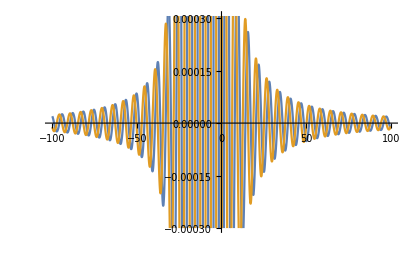

```mathematica
Plot[Evaluate@ReIm[xintIP[τ]],{τ,-100,100}]
```

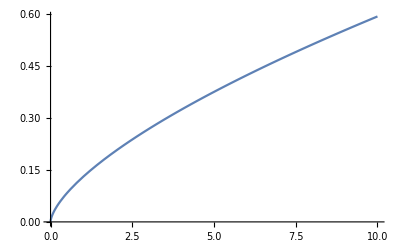

```mathematica
Plot[Im[1/GLargeNf-(-kxv+ⅈ ω)]/.{Nfkfv->1/100,kxv->0},{ω,0,10}]
```

```mathematica
Nfs={100,.01(*,1,.1,10*)};
ωm=10;
n=2^10;
ωs=Subdivide[-ωm,ωm,n-1];
Do[
f=OpenWrite[NotebookDirectory[]<>"benchmarkRefOutput/benchmarkRef3_Nf="<>ToString[If[Nfkfv∈Integers,Nfkfv,N@Nfkfv]],BinaryFormat->True];
BinaryWrite[f,n,"Integer32"];
BinaryWrite[f,ωm,"Real64"];
BinaryWrite[f,Flatten@ParallelTable[N[GLargeNfv1[ω,kxv,Nfkfv],40],{ω,ωs},{kxv,ωs}],"Complex128"];
Close[f];
,{Nfkfv,Nfs}]
```

```mathematica
(2.π)^2
```

39.4784

```mathematica
Limit[GLargeNf,Nfkfv->∞]
```

1/(-kxv+ⅈ ω)

```mathematica
n=2^7;
ωs=Subdivide[-ωm,ωm,n-1];
bb=ParallelTable[N[GLargeNf/.Nfkfv->1/100,20],{ω,ωs},{kxv,ωs}];
```

```mathematica
n=2^7;
ωs=Subdivide[-ωm,ωm,n-1];
aa=ParallelTable[N[1/GLargeNf-(-kxv+ⅈ ω)/.Nfkfv->1/100,20],{ω,ωs},{kxv,ωs}];
```

```mathematica
ListPlot3D[Re[bb]]
```

-Graphics3D-

```mathematica
aa[[1,1]]
```

-0.50545762924729886453-0.2834131038166370972 ⅈ

```mathematica
ListPlot3D[Im[aa]]
```

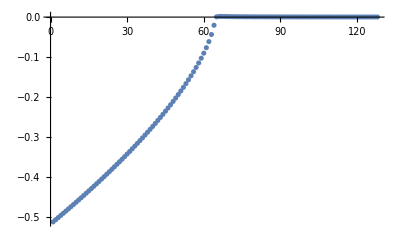

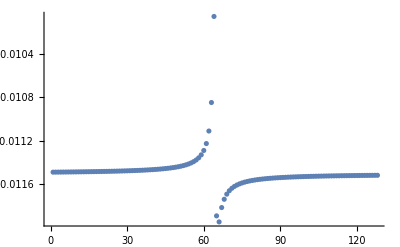

```mathematica
ListPlot[Re[aa[[;;,66]]]]
ListPlot[Im[aa[[64,;;]]],PlotRange->All]
```

```mathematica
ωm=1000;
n=1000;
kxt=1;
ωs=Subdivide[-ωm,ωm,n-1];
Gs=ParallelTable[1/GLargeNfv1[ω,kxt,1]-1/Gf0[ω,kxt]/.v->1,{ω,ωs}];
```

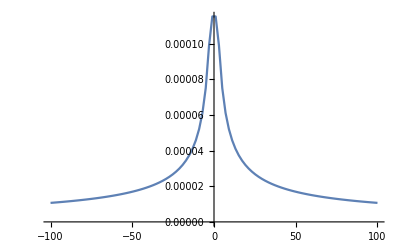

```mathematica
ListLinePlot[{{ωs,Re[Gs]}ᵀ},PlotRange->All,PlotRange->{-.01,.01}]
```

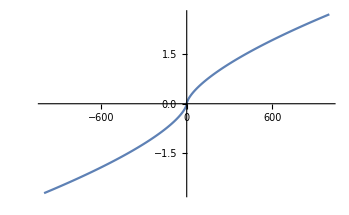

```mathematica
ListLinePlot[{{ωs,Im[Gs]}ᵀ},PlotRange->All]
```